Note: In this problem set, expressions in green cells match corresponding expressions in the text answers.

```mathematica
ClearAll["Global`*"]
```

1.  Lots of kitchen knives are inspected by a sampling plan that uses a sample of size 20 and the acceptance number c = 1. What is the probability of accepting a lot with 1%, 2%, 10% defectives (knives with dull blades)? Use table A6 of the Poisson distribution in appendix 5. Graph the OC curve.

Lot of knives with 1% defective

```mathematica
prob=NProbability[n≤1,n\[Distributed]PoissonDistribution[20 0.01]]
```

0.982477

Lot of knives with 2% defective

```mathematica
prob=NProbability[n≤1,n\[Distributed]PoissonDistribution[20 0.02]]
```

0.938448

Lot of knives with 10% defective

```mathematica
prob=NProbability[n≤1,n\[Distributed]PoissonDistribution[20 0.1]]
```

0.406006

```mathematica
DiscretePlot[PrimePi[k],{k,1,50}]
```

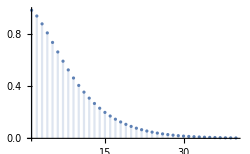

```mathematica
DiscretePlot[NProbability[n≤1,n\[Distributed]PoissonDistribution[20 0.01 k]],{k,1,40},ImageSize->250]
```

3.  How will the probabilities in problem 1 with n = 20 change (up or down) if we decrease c to zero? First guess.

```mathematica
prob=NProbability[n==0,n\[Distributed]PoissonDistribution[20 0.01]]
```

0.818731

```mathematica
prob=NProbability[n==0,n\[Distributed]PoissonDistribution[20 0.02]]
```

0.67032

```mathematica
prob=NProbability[n==0,n\[Distributed]PoissonDistribution[20 0.1]]
```

0.135335

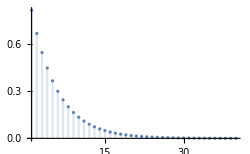

```mathematica
DiscretePlot[NProbability[n==0,n\[Distributed]PoissonDistribution[20 0.01 k]],{k,1,40},ImageSize->250,PlotRange->All]
```

5.  Lots of copper pipes are inspected according to a sample plan that uses sample size 25 and acceptance number 1. Graph the OC curve of the plan, using the poisson approximation. Find the producer’s risk if the AQL is 1.5%.

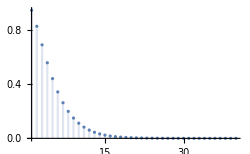

```mathematica
DiscretePlot[NProbability[n≤1,n\[Distributed]PoissonDistribution[25 0.015 k]],{k,1,40},ImageSize->250,PlotRange->All]
```

```mathematica
NProbability[n≤1,n\[Distributed]PoissonDistribution[25 0.015 ]]
```

0.945023

The answer in the green cell matches the answer in the text. At the very first k, with the probability at 94.5%, the α or producer’s risk must be the remainder,

```mathematica
1-%
```

0.0549772

The text answer quotes this as 5.5%, close enough for 3S agreement.

7.  In example 1 in the text, what are the producer’s and consumer’s risks if the AQL is 0.1 and the RQL is 0.6?

```mathematica
rid=N[Table[((20-20 θ)(19-20 θ))/380,{θ,0,1,0.05}]]
```

{1.,0.9,0.805263,0.715789,0.631579,0.552632,0.478947,0.410526,0.347368,0.289474,0.236842,0.189474,0.147368,0.110526,0.0789474,0.0526316,0.0315789,0.0157895,0.00526316,0.,0.}

```mathematica
hit=Range[21]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21}

```mathematica
duo=Table[{hit[[n]],rid[[n]]},{n,1,21}]
```

{{1,1.},{2,0.9},{3,0.805263},{4,0.715789},{5,0.631579},{6,0.552632},{7,0.478947},{8,0.410526},{9,0.347368},{10,0.289474},{11,0.236842},{12,0.189474},{13,0.147368},{14,0.110526},{15,0.0789474},{16,0.0526316},{17,0.0315789},{18,0.0157895},{19,0.00526316},{20,0.},{21,0.}}

The plot below shows the function which relates to example 1. The table ‘duo’ contains the probabilities for each point in the plot.

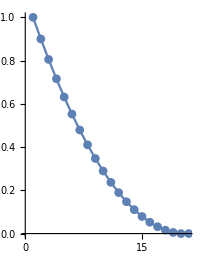

```mathematica
ListLinePlot[duo,AspectRatio->1.3,ImageSize->200,PlotMarkers->Automatic]
```

Looking at the table ‘rid’, I see from its index that θ=0.1, which will be the AQL, has a function value of 0.805263, and the α will equal

```mathematica
1-0.805263
```

0.194737

Similarly, 0.147368 is the function value when θ = 0.6, leading to

```mathematica
0.147368
```

The green cells above match the answer in the text to 3S.

9.  Graph and compare sampling plans with c = 1 and increasing values of n, say, n = 2, 3, 4. (Use the binomial distribution.)

Like in example 1, I will vary the probability of discovering a defective in twenty steps from 0 to 1. First, n = 2.

```mathematica
n2=Table[NProbability[x≤1,x\[Distributed]BinomialDistribution[2,n ]],{n,0,1,0.05}];
```

```mathematica
d2=Range[21];
```

```mathematica
duo2=Table[{d2[[n]],n2[[n]]},{n,1,21}];
```

```mathematica
p2=ListLinePlot[duo2,AspectRatio->1.3,ImageSize->200,PlotMarkers->Automatic,PlotStyle->Red];
```

Then I will move on to n = 3.

```mathematica
n3=Table[NProbability[x≤1,x\[Distributed]BinomialDistribution[3,n ]],{n,0,1,0.05}];
```

```mathematica
duo3=Table[{d2[[n]],n3[[n]]},{n,1,21}]
```

{{1,1.},{2,0.99275},{3,0.972},{4,0.93925},{5,0.896},{6,0.84375},{7,0.784},{8,0.71825},{9,0.648},{10,0.57475},{11,0.5},{12,0.42525},{13,0.352},{14,0.28175},{15,0.216},{16,0.15625},{17,0.104},{18,0.06075},{19,0.028},{20,0.00725},{21,0.}}

```mathematica
p3=ListLinePlot[duo3,AspectRatio->1.3,ImageSize->200,PlotMarkers->Automatic,PlotStyle->Green];
```

Finally I will make one for n = 4.

```mathematica
n4=Table[NProbability[x≤1,x\[Distributed]BinomialDistribution[4,n ]],{n,0,1,0.05}];
```

```mathematica
duo4=Table[{d2[[n]],n4[[n]]},{n,1,21}];
```

```mathematica
p4=ListLinePlot[duo4,AspectRatio->1.3,ImageSize->200,PlotMarkers->Automatic,PlotStyle->Blue];
```

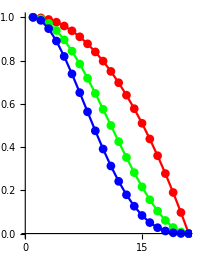

```mathematica
Show[p2,p3,p4]
```

11. Samples of 3 fuses are drawn from lots and a lot is accepted if in the corresponding sample we find no more than 1 defective fuse. Criticize this sampling plan. In particular, find the probability of accepting a lot that is 50% defective. (Use the binomial distribution, as shown in numbered line (7), section 24.7).

If the lot of fuses has a 50% chance of being defective, and a sample of 3 is drawn from it, there is a 50-50 chance that no more than 1 defective fuse will be found in the sample, though half the fuses in the lot are bad.

```mathematica
prob=NProbability[n≤1,n\[Distributed]BinomialDistribution[3,0.5]]
```

0.5

12. If in a sampling plan for large lots of spark plugs, the sample size is 100 and we want the AQL to be 5% and the producer’s risk 2%, what acceptance number c should we choose? (Use the normal approximation of the binomial distribution in section 24.8).

13. What is the consumer’s risk in problem 12 if we want the RQL to be 12%? Use c = 9 from the answer of problem 12.

This seemed hard to grasp. I wanted to make a plot but it slowed down my machine to a molasses speed. I looked into the normal approximation of the binomial, as the problem description instructs, but it is complicated, and the parameters of the present problem seem to lie on the lower cusp anyway in terms of the justification for the approximation. The following table, ‘n11’, would normally show 101 function values between 0 and 1, but I have the variable n throttled so that it only shows 21 values, going up to 0.2. The thirteenth one, the one that corresponds to the 12% location of θ, is 0.225652. Therefore I believe that value corresponds to the consumer’s risk which was asked for. Since I did not use the normal distribution approximation method, it may even be more exact than the text answer (which is 22%).

```mathematica
n11=Table[NProbability[x≤9,x\[Distributed]BinomialDistribution[100,n ]],{n,0,0.2,0.01}]
```

{1.,1.,0.999966,0.999126,0.993156,0.971812,0.922461,0.83798,0.721978,0.587506,0.45129,0.327753,0.225652,0.147726,0.0922424,0.0550946,0.0315594,0.017378,0.00921743,0.00471767,0.00233356}

```mathematica
Length[n11]
```

101

```mathematica
d11=Range[101];
```

```mathematica
duo11=Table[{d11[[n]],n11[[n]]},{n,1,101}];
```

```mathematica
p11=ListLinePlot[duo11,AspectRatio->150,ImageSize->150,PlotMarkers->Automatic,PlotStyle->RGBColor[0.2,0.6,0.2],PlotRange->{{0,105},{0,.005}},ImagePadding->25];
```

Warning, plot in above cell is very demanding of resources.

15. Graph the OC curve and the AOQ curve for the single sampling plan for large lots with n = 5 and c = 0, and find the AOQL.

According to numbered line (2) on p. 1092 the probability of P(A; θ) looks like
P(A; θ)=Sum[((N θ
x)(N-N θ
n-x))/(N
n),{x,0,c}] where N is the number in the lot and n is the number in the inspection sample. What is unclear is that, with c = 0, does this sum mean anything?

```mathematica
Sum[x,{x,0,0}]
```

0

The portents do not seem favorable. I think I should plot a sampling plan and take a look at it, to see if it gives me any ideas.

```mathematica
n5=Table[NProbability[x==0,x\[Distributed]BinomialDistribution[5,n ]],{n,0,1,0.05}];
```

```mathematica
d5=Range[21];
```

```mathematica
duo5=Table[{d5[[n]],n5[[n]]},{n,1,21}]
```

{{1,1.},{2,0.773781},{3,0.59049},{4,0.443705},{5,0.32768},{6,0.237305},{7,0.16807},{8,0.116029},{9,0.07776},{10,0.0503284},{11,0.03125},{12,0.0184528},{13,0.01024},{14,0.00525219},{15,0.00243},{16,0.000976563},{17,0.00032},{18,0.0000759375},{19,0.00001},{20,3.125×10^-7},{21,0.}}

According to numbered line (4) on p. 1095, AOQ[θ]=θ P(A; θ), so I can stick in a θ, that is, an n, into the formula.

```mathematica
n6=Table[n NProbability[x==0,x\[Distributed]BinomialDistribution[5,n ]],{n,0,1,0.05}]
```

{0.,0.038689,0.059049,0.0665558,0.065536,0.0593262,0.050421,0.0406102,0.031104,0.0226478,0.015625,0.010149,0.006144,0.00341392,0.001701,0.000732422,0.000256,0.0000645469,9.×10^-6,2.96875×10^-7,0.}

```mathematica
duo6=Table[{d5[[n]],n6[[n]]},{n,1,21}]
```

{{1,0.},{2,0.038689},{3,0.059049},{4,0.0665558},{5,0.065536},{6,0.0593262},{7,0.050421},{8,0.0406102},{9,0.031104},{10,0.0226478},{11,0.015625},{12,0.010149},{13,0.006144},{14,0.00341392},{15,0.001701},{16,0.000732422},{17,0.000256},{18,0.0000645469},{19,9.×10^-6},{20,2.96875×10^-7},{21,0.}}

```mathematica
Max[n6]
```

0.0665558

The green cell above matches the answer in the text for AOQL, i.e. 6.7%.

```mathematica
p5=ListLinePlot[duo5,AspectRatio->1.3,ImageSize->300,PlotMarkers->Automatic,PlotStyle->Brown,GridLines->All];
```

```mathematica
p6=ListLinePlot[duo6,AspectRatio->1.3,ImageSize->300,PlotMarkers->Automatic,PlotStyle->RGBColor[0.9,0.7,0.2]];
```

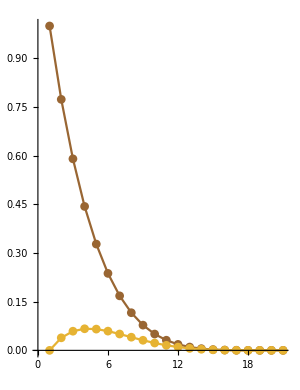

```mathematica
Show[p5,p6]
```